```mathematica
myThickness=0.005;
tickFunc=Charting`ScaledTicks[{Identity,Identity},TicksLength->{.03,.015}][##]&;
g[x_,s_,r_,i_,α_]:=s-r-i x^(1/α);  
f[x_,s_,r_,i_,α_]:=s(1-s)g[x,s,r,i,α];
sx[x_,r_,i_,α_]:=r+i x^(1/α);
```

```mathematica
alfa=0.25;r0=0.15;p=0.7;i0=p-r0;
```

```mathematica
A - scenario
```

A-scenario

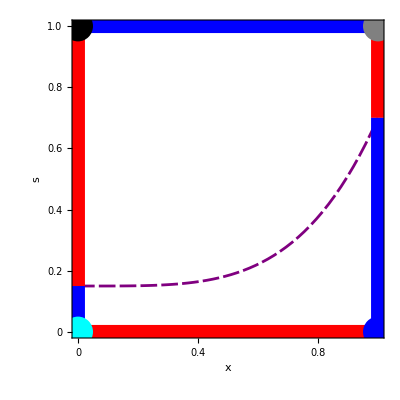

```mathematica
pl12=Plot[{sx[x,r0,i0,alfa]},{x,0.0,1.0},
PlotStyle->{{Thickness[myThickness],Purple,AbsoluteDashing[{12,3}]},{Thickness[myThickness],Black,AbsoluteDashing[{12,3}]},{Thickness[myThickness],Blue,AbsoluteDashing[{12,3}]}},
ImagePadding->All,Frame->True,
FrameTicks->{{tickFunc,tickFunc},{tickFunc,tickFunc}},
FrameLabel->{"x","s"},
Ticks->Automatic,
LabelStyle->Directive[FontFamily->"Helvetica",Black,Bold,16],
AspectRatio->1,
PlotRange->{{0,1},{0,1}}];
pl02=Plot[{},{x,0.0,1.0},
PlotStyle->{{Thickness[myThickness],Purple,AbsoluteDashing[{12,3}]},{Thickness[myThickness],Black,AbsoluteDashing[{12,3}]},{Thickness[myThickness],Blue,AbsoluteDashing[{12,3}]}},
ImagePadding->All,Frame->True,
FrameTicks->{{tickFunc,tickFunc},{tickFunc,tickFunc}},
FrameLabel->{"x","s"},
Ticks->Automatic,
LabelStyle->Directive[FontFamily->"Helvetica",Black,Bold,16],
AspectRatio->1,
PlotRange->{{0,1},{0,1}}];
topA={Arrowheads[0.12],Arrow[{{0,1},{1,1}}]};
topB={Arrowheads[0.12],Arrow[{{1,1},{0,1}}]};
bot={Arrowheads[0.12],Arrow[{{1,0},{0,0}}]};
lup={Arrowheads[0.12],Arrow[{{0,r0},{0,1}}]};
ldo={Arrowheads[0.12],Arrow[{{0,r0},{0,0}}]};
rup={Arrowheads[0.12],Arrow[{{1,p},{1,1}}]};
rdo={Arrowheads[0.12],Arrow[{{1,p},{1,0}}]};
pltopA=Graphics[{Thickness[0.025],Blue,topA}];
pltopB=Graphics[{Thickness[0.025],Red,topB}];
plbot=Graphics[{Thickness[0.025],Red,bot}];
pllup=Graphics[{Thickness[0.025],Red,lup}];
plldo=Graphics[{Thickness[0.025],Blue,ldo}];
plrup=Graphics[{Thickness[0.025],Red,rup}];
plrdo=Graphics[{Thickness[0.025],Blue,rdo}];
pl00=Graphics[{Cyan,Disk[{0,0},0.05]}];
pl01=Graphics[{Black,Disk[{0,1},0.05]}];
pl11=Graphics[{Gray,Disk[{1,1},0.05]}];
pl10=Graphics[{Blue,Disk[{1,0},0.05]}];
q21=Show[pl12,pltopA,plbot,pllup,plldo,plrup,plrdo,pl02,pl00,pl01,pl11,pl10]
```

```mathematica
B - scenario
```

B-scenario

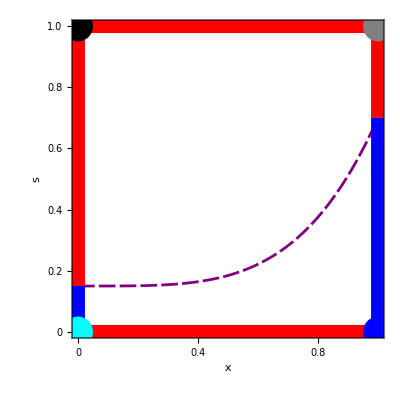

```mathematica
(***           behavior of s(x,λ,p,α,r) for x=1 while changing p for constant λ and α                  ***)
pl12=Plot[{sx[x,r0,i0,alfa]},{x,0.0,1.0},
PlotStyle->{{Thickness[myThickness],Purple,AbsoluteDashing[{12,3}]},{Thickness[myThickness],Black,AbsoluteDashing[{12,3}]},{Thickness[myThickness],Blue,AbsoluteDashing[{12,3}]}},
ImagePadding->All,Frame->True,
FrameTicks->{{tickFunc,tickFunc},{tickFunc,tickFunc}},
FrameLabel->{"x","s"},
Ticks->Automatic,
LabelStyle->Directive[FontFamily->"Helvetica",Black,Bold,16],
AspectRatio->1,
PlotRange->{{0,1},{0,1}}];
pl02=Plot[{},{x,0.0,1.0},
PlotStyle->{{Thickness[myThickness],Red,AbsoluteDashing[{12,3}]},{Thickness[myThickness],Black,AbsoluteDashing[{12,3}]},{Thickness[myThickness],Blue,AbsoluteDashing[{12,3}]}},
ImagePadding->All,Frame->True,
FrameTicks->{{tickFunc,tickFunc},{tickFunc,tickFunc}},
FrameLabel->{"x","s"},
Ticks->Automatic,
LabelStyle->Directive[FontFamily->"Helvetica",Black,Bold,16],
AspectRatio->1,
PlotRange->{{0,1},{0,1}}];
topA={Arrowheads[0.12],Arrow[{{0,1},{1,1}}]};
topB={Arrowheads[0.12],Arrow[{{1,1},{0,1}}]};
bot={Arrowheads[0.12],Arrow[{{1,0},{0,0}}]};
lup={Arrowheads[0.12],Arrow[{{0,r0},{0,1}}]};
ldo={Arrowheads[0.12],Arrow[{{0,r0},{0,0}}]};
rup={Arrowheads[0.12],Arrow[{{1,p},{1,1}}]};
rdo={Arrowheads[0.12],Arrow[{{1,p},{1,0}}]};
pltopA=Graphics[{Thickness[0.025],Blue,topA}];
pltopB=Graphics[{Thickness[0.025],Red,topB}];
plbot=Graphics[{Thickness[0.025],Red,bot}];
pllup=Graphics[{Thickness[0.025],Red,lup}];
plldo=Graphics[{Thickness[0.025],Blue,ldo}];
plrup=Graphics[{Thickness[0.025],Red,rup}];
plrdo=Graphics[{Thickness[0.025],Blue,rdo}];
pl00=Graphics[{Cyan,Disk[{0,0},0.05]}];
pl01=Graphics[{Black,Disk[{0,1},0.05]}];
pl11=Graphics[{Gray,Disk[{1,1},0.05]}];
pl10=Graphics[{Blue,Disk[{1,0},0.05]}];
q22=Show[pl12,pltopB,plbot,pllup,plldo,plrup,plrdo,pl02,pl02,pl00,pl01,pl11,pl10]
```

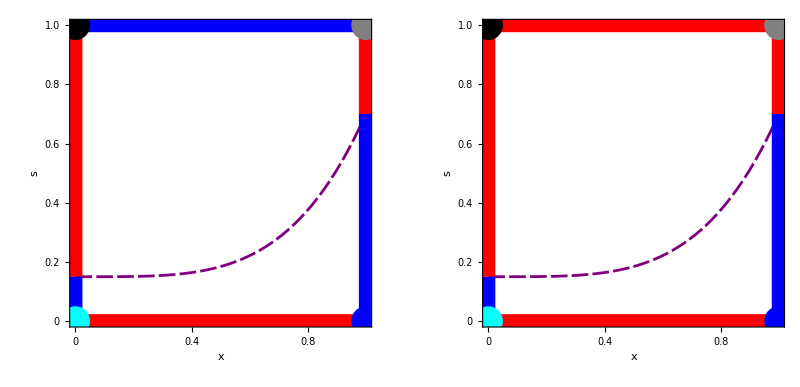

```mathematica
GraphicsGrid[{{q21,q22}}]
```